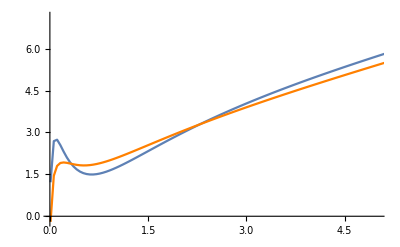

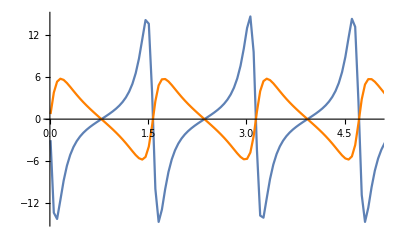

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.80qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Re[βpz[i,1.2qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,1.20qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
]
```

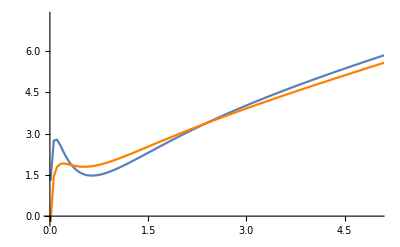

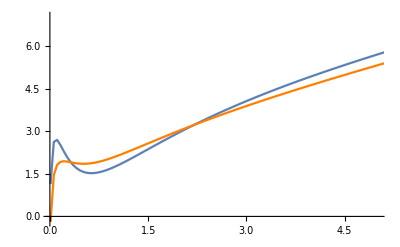

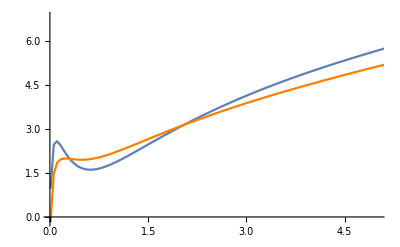

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0.8,2,0.75μextreme[0.8,2]],0.1,0.8,2,0.75μextreme[0.8,2]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0.8,2,0.75μextreme[0.8,2]],0.1,0.8,2,0.75μextreme[0.8,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1.2,2,0.75μextreme[1.2,2]],0.1,1.2,2,0.75μextreme[1.2,2]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1.2,2,0.75μextreme[1.2,2]],0.1,1.2,2,0.75μextreme[1.2,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1.6,2,0.75μextreme[1.6,2]],0.1,1.6,2,0.75μextreme[1.6,2]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1.6,2,0.75μextreme[1.6,2]],0.1,1.6,2,0.75μextreme[1.6,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
]
```

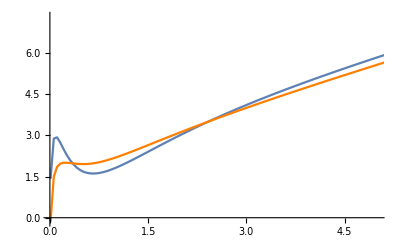

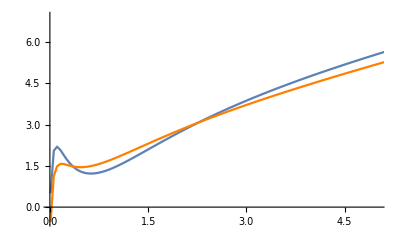

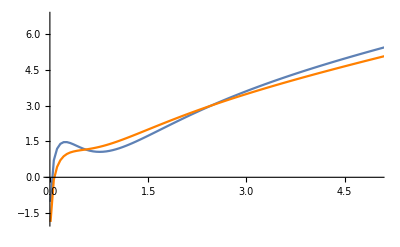

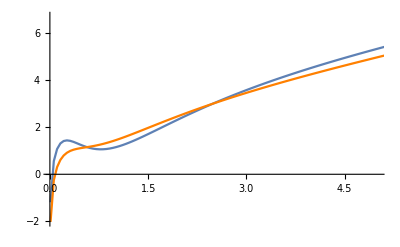

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1,1,0.75μextreme[1,1]],0.1,1,1,0.75μextreme[1,1]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1,1,0.75μextreme[1,1]],0.1,1,1,0.75μextreme[1,1]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1,10,0.75μextreme[1,10]],0.1,1,10,0.75μextreme[1,10]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1,10,0.75μextreme[1,10]],0.1,1,10,0.75μextreme[1,10]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1,100,0.75μextreme[1,100]],0.1,1,100,0.75μextreme[1,100]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1,100,0.75μextreme[1,100]],0.1,1,100,0.75μextreme[1,100]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,1,1000,0.75μextreme[1,1000]],0.1,1,1000,0.75μextreme[1,1000]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1,1000,0.75μextreme[1,1000]],0.1,1,1000,0.75μextreme[1,1000]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
PlotRange->{{0.01,5},All},AxesOrigin->{0,0}
]];
]
```

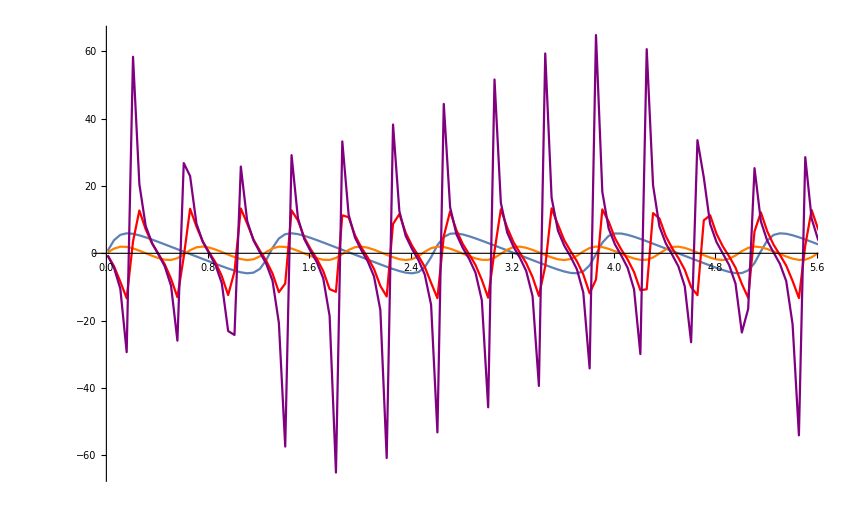

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,1,0.75μextreme[1.2247,1]],0.1,1.2247,1,0.75μextreme[1.2247,1]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,10,0.75μextreme[1.2247,10]],0.1,1.2247,10,0.75μextreme[1.2247,10]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,100,0.75μextreme[1.2247,100]],0.1,1.2247,100,0.75μextreme[1.2247,100]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,1000,0.75μextreme[1.2247,1000]],0.1,1.2247,1000,0.75μextreme[1.2247,1000]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```

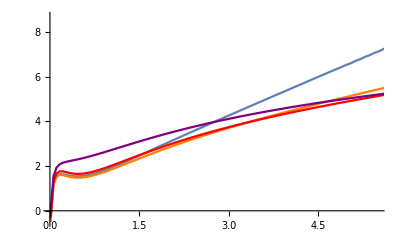

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,0.8qcrit[0.1,0.612,10,0.75μextreme[0.612,10]],0.1,0.612,10,0.75μextreme[1.2247,10]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,0.8qcrit[0.1,1.2247,10,0.75μextreme[1.2247,10]],0.1,1.2247,10,0.75μextreme[1.2247,10]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Re[pz[i,0.8qcrit[0.1,1.8371,10,0.75μextreme[1.8371,10]],0.1,1.8371,10,0.75μextreme[1.8371,10]]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,0.8qcrit[0.1,2.4249,10,0.75μextreme[2.4249,10]],0.1,2.4249,10,0.75μextreme[2.4249,10]]]//Log},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```

```mathematica
{0.25Sqrt[6],0.5Sqrt[6],0.75Sqrt[6],0.99Sqrt[6]}//N
```

{0.612372,1.22474,1.83712,2.42499}

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Table[{i,βpz[i,0.8qcrit[0.1,1,10,0.75μextreme[1,10]],0.1,1,10,0.75μextreme[1,10]]},{i,0.01,7,0.05}]];
]
```

{{0.01,-1.65203},{0.06,-7.74253},{0.11,-8.98757},{0.16,-7.96426},{0.21,-6.65224},{0.26,-5.59673},{0.31,-4.8335},{0.36,-4.29793},{0.41,-3.92735},{0.46,-3.67642},{0.51,-3.51446},{0.56,-3.42093},{0.61,-3.38204},{0.66,-3.38842},{0.71,-3.43369},{0.76,-3.5135},{0.81,-3.62491},{0.86,-3.766},{0.91,-3.93558},{0.96,-4.133},{1.01,-4.35802},{1.06,-4.61072},{1.11,-4.8914},{1.16,-5.20058},{1.21,-5.53894},{1.26,-5.90725},{1.31,-6.30642},{1.36,-6.73743},{1.41,-7.20136},{1.46,-7.69932},{1.51,-8.23252},{1.56,-8.80218},{1.61,-9.4096},{1.66,-10.0561},{1.71,-10.7431},{1.76,-11.472},{1.81,-12.2442},{1.86,-13.0612},{1.91,-13.9246},{1.96,-14.836},{2.01,-15.7968},{2.06,-16.8089},{2.11,-17.8738},{2.16,-18.9933},{2.21,-20.1691},{2.26,-21.4031},{2.31,-22.697},{2.36,-24.0528},{2.41,-25.4725},{2.46,-26.9579},{2.51,-28.5112},{2.56,-30.1344},{2.61,-31.8297},{2.66,-33.5993},{2.71,-35.4453},{2.76,-37.3694},{2.81,-39.3762},{2.86,-41.4651},{2.91,-43.6415},{2.96,-45.9066},{3.01,-48.262},{3.06,-50.7139},{3.11,-53.2599},{3.16,-55.9087},{3.21,-58.6573},{3.26,-61.5161},{3.31,-64.4903},{3.36,-67.5598},{3.41,-70.7557},{3.46,-74.0674},{3.51,-77.5026},{3.56,-81.0663},{3.61,-84.7617},{3.66,-88.5901},{3.71,-92.5555},{3.76,-96.665},{3.81,-100.923},{3.86,-105.332},{3.91,-109.896},{3.96,-114.633},{4.01,-119.522},{4.06,-124.576},{4.11,-129.818},{4.16,-135.238},{4.21,-140.846},{4.26,-146.651},{4.31,-152.65},{4.36,-158.858},{4.41,-165.283},{4.46,-171.913},{4.51,-178.775},{4.56,-185.871},{4.61,-193.204},{4.66,-200.791},{4.71,-208.631},{4.76,-216.722},{4.81,-225.098},{4.86,-233.751},{4.91,-242.683},{4.96,-251.933},{5.01,-261.479},{5.06,-271.325},{5.11,-281.522},{5.16,-292.05},{5.21,-302.913},{5.26,-314.155},{5.31,-325.761},{5.36,-337.736},{5.41,-350.129},{5.46,-362.922},{5.51,-376.112},{5.56,-389.764},{5.61,-403.858},{5.66,-418.395},{5.71,-433.437},{5.76,-448.965},{5.81,-464.971},{5.86,-481.537},{5.91,-498.639},{5.96,-516.267},{6.01,-534.59},{6.06,-553.565},{6.11,-572.916},{6.16,-592.798},{6.21,-613.039},{6.26,-633.984},{6.31,-656.525},{6.36,-679.847},{6.41,-702.345},{6.46,-726.08},{6.51,-752.241},{6.56,-778.791},{6.61,-804.74},{6.66,-832.16},{6.71,-861.564},{6.76,-891.884},{6.81,-923.5},{6.86,-953.253},{6.91,-984.654},{6.96,-1018.11}}